# Unit 1: Derivatives

## What is a derivative?

### Rate of Change

```mathematica
220-50
```

170

```mathematica
170/2
```

85

### Average vs. Instantaneous

(Delta f)/(Delta t)

```mathematica
1/(1/60)
```

60

### Instantaneous approximation continued

```mathematica
(220000-210000)/(32-30)
```

5000

### Derivative at a point

The Derivative of f(x) at x = a  
f.b4(a) = Lim_(b→a) (f(b)-f(a))/(b-a)

### A negative derivative?

```mathematica
f[t_] := 100 +20t-5 t^2
f'[2]
```

0

## Geometric interpretation of the derivative

### Tangent lines

Calculated using:
y-f(a)=m(x-a)

### Equation of a tangent line

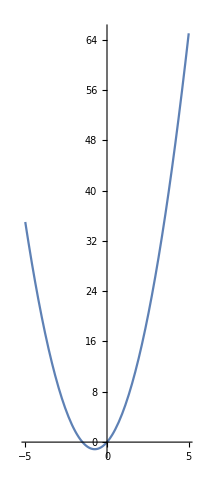

5

```mathematica
j[x_]:= 2 x^2+3x
Plot[j[x],{x,-5,5}, AspectRatio->Full]
j[1]
```

```mathematica
j'[1]
```

7

```mathematica
j[1]
```

5

```mathematica
Simplify[y-j[1]==j'[1] * (x-1)]
```

7 x==2+y

#### Review questions

```mathematica
f[x_]:=-2x+1
f[3]
```

-5

## Calculating derivatives

### Linearity

h[x_]:= 1/x^2
h'[x_]:=lim_(Δx→ 0) (1/(x^2+Δx)-1/x^2)/Δx
h'[x_]:=lim_(Δx→ 0) -2/x^3

```mathematica
h[x_]:= 1/x^2
h'[s]
```

-2/s^3

### Relationship between derivatives

```mathematica
f[x_]:=-3/x
f'[x]
```

3/x^2

### Calculation

```mathematica
f[x_]:=4 √x-3/x^2
f'[x]
```

6/x^3+2/(√x)

## Leibniz notation

dy/dx     or   df/dx

### Area of a circle

```mathematica
A[r_] :=π r^2
A'[r]
A'[3]
```

2 π r

6 π

```mathematica
A2[c_]:=π *(c-2*π)^2
A2'[c]
A2'[6π]
```

2 (c-2 π) π

8 π^2

### exercise

```mathematica
D[g^3+2 g^2, g] /.g->2 
f[x_] := x^3+2 x^2
f'[2]

3*2^2+4*2
```

20

20

20

## Second derivatives and higher

everything lost do to power outage

# Homework

## Part A

## Velocity

```mathematica
h[x_]:= 400-16 x^2
(h[0]-h[2])/(0-2)

Solve[h[g]==0,g]
(h[3]-h[5])/(3-5)

h'[5]
```

-32

{{g→-5},{g→5}}

-128

-160

## Definition review

```mathematica
f[x_]:=1/(2x+1)
f'[x]
```

-2/(1+2 x)^2

```mathematica
N[Solve[f'[x]==1,x, Reals]]
N[Solve[f'[x]==0,x, Reals]]
N[Solve[f'[x]==-1,x, Reals]]
```

{}

{}

{{x→-1.20711},{x→0.207107}}

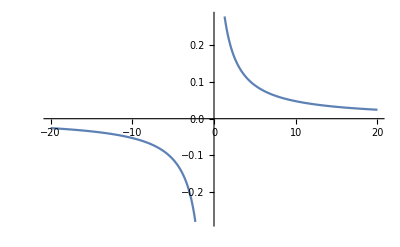

```mathematica
Plot[f[x],{x,-20,20}]
```

```mathematica
g[x_]:=4x+5
N[Solve[g[x]==1,x, Reals]]
N[Solve[g[x]==0,x, Reals]]
N[Solve[g[x]==-1,x, Reals]]
```

{{x→-1.}}

{{x→-1.25}}

{{x→-1.5}}

```mathematica
j[x_]:=x^(-7/4)
j'[1]
```

-7/4

## Tangent line

```mathematica
f[x_]:=1/(2x+1)
m :=f'[1]
b :=(-1)*(m*1-f[1])
y=m*x+b
```

5/9-(2 x)/9

## Differentiability

```mathematica
Piecewise[{{c*x^2+4x+1, x≥1}, {a*x+b, x<1}}]
```

Piecewise[{{1+4 x+c x^2, x≥1}, {b+a x, x<1}, {0, True}}]

```mathematica
x=1;
c*x^2+4*x+1==a*x+b
```

5+c==a+b

```mathematica
2*c*x+4==a
```

4+2 c==a

```mathematica
5+c-(4+2c)==b
```

1-c==b

## Differentiability 2

```mathematica
f[x_]:=Piecewise[{{a*x+b, x>0}, {Sin[x], x≤ 0}}]
Plot[f[x],{x,0,20}]
```

-Graphics-

```mathematica
Sin[0]
```

0

## Polynomials

```mathematica
D[x^10+3 x^5+2 x^3+4,x]
```

6 x^2+15 x^4+10 x^9

```mathematica
p[x_]=Integrate[x^6+5 x^5+4 x^3,x] + 1
```

1+x^4+(5 x^6)/6+x^7/7

```mathematica
f[x_]:=Piecewise[{{a*+x^2+b*x+4, x≤1}, {5*x^5+3*x^4+7*x^2+8*x+4, x>1}}]
```

```mathematica
x=1;
a*+x^2+b*x+4==5*x^5+3*x^4+7*x^2+8*x+4
D[a*+y^2+b*y+4,y]
D[5*y^5+3*y^4+7*y^2+8*y+4,y]
b+2 a x == 8+14 x+12 x^3+25 x^4
```

4+a+b==27

b+2 a y

8+14 y+12 y^3+25 y^4

2 a+b==59

```mathematica
Solve[4+a+b==27&& 2 a+b==59,{a,b}]
```

{{a→36,b→-13}}

## Second derivatives

```mathematica
D[3 x^2+2x+4*√x,{x,2}]
```

6-1/x^(3/2)

```mathematica
D[-5/x+5,{x,2}]
```

-10/x^3

```mathematica
D[(x^2+5x)/(x+5),{x,2}]
```

2/(5+x)-(2 (5+2 x))/(5+x)^2+(2 (5 x+x^2))/(5+x)^3

## Trig

```mathematica
D[Sin[x],{x,103}]
```

-Cos[x]

## Part B

## Speedometer

```mathematica
a = 1*π /0.08*3.6
p = .22*π /0.08*3.6
```

141.372

31.1018

```mathematica
Abs[p-a]/a
```

0.78

```mathematica
f1[x_]:= d*π /0.08*3.6
Solve[Abs[p-f1[d]]/f1[d]==0.05,d]
```

{{d→0.209524},{d→0.231579}}

```mathematica
Abs[0.20952380952380942-.22]
```

0.0104762

## Skate Park

```mathematica
f[x_,a_,b_,c_]:=a*x^2+b*x+c
f2[x_,a_,b_]:= b+2 *a*x
Solve[f[2,a,b,c]==1 && f[4,a,b,c]==3 && f2[2,a,b]==-1/4 ,{a,b,c}]
```

{{a→5/8,b→-11/4,c→4}}

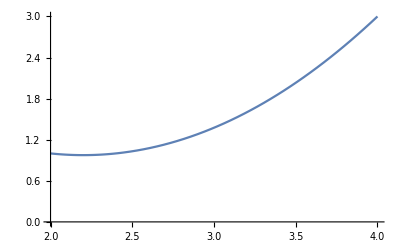

```mathematica
res[x_]:= 5/8 x^2-11/4*x+4
Plot[res[x],{x,2,4}, PlotRange->{0,3}]
```